```mathematica
SetDirectory[NotebookDirectory[]];
g01=Import["data/parity_thermal_g01.csv"][[2;;]];
g02=Import["data/parity_thermal_g02.csv"][[2;;]];
g12=Import["data/parity_thermal_g12.csv"][[2;;]];
dd=Import["data/parity_thermal_dd.csv"][[2;;]];
q=Import["data/parity_thermal_q.csv"][[2;;]];
myStyle[size_]:=Directive[FontFamily->"Times New Roman",size,Black];
```

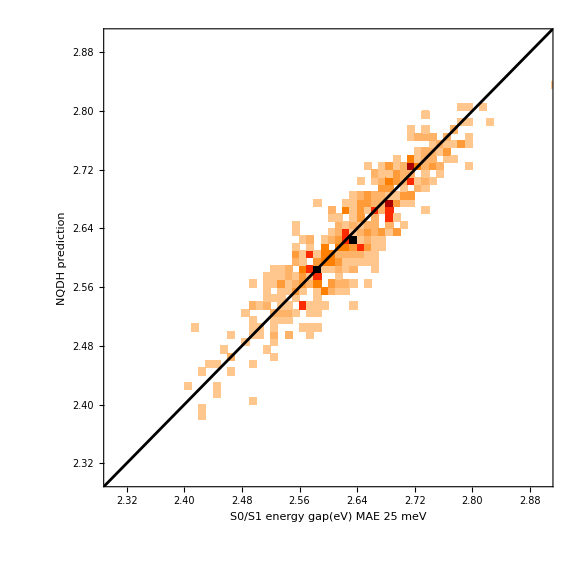

```mathematica
Show[
DensityHistogram[
g01,
50,
FrameStyle->myStyle[30],
FrameLabel->Table[Style[text,myStyle[30]],{text,{"S0/S1 energy gap(eV)\nMAE 25 meV","NQDH prediction"}}],
ImageSize->Large,
PlotRange->{{2.3,2.9},{2.3,2.9}},
ColorFunction->(Blend[{Lighter[Lighter[Orange]],Lighter[Orange],Orange,Red,Black},#]&)
],
Plot[x,{x,-100,100},PlotStyle->Black]
]
```

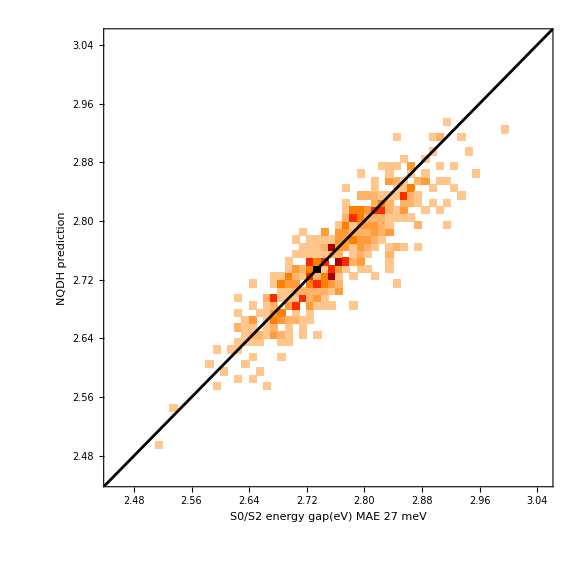

```mathematica
Show[
DensityHistogram[
g02,
50,
FrameStyle->myStyle[30],
FrameLabel->Table[Style[text,myStyle[30]],{text,{"S0/S2 energy gap(eV)\nMAE 27 meV","NQDH prediction"}}],
ImageSize->Large,
PlotRange->{{2.45,3.05},{2.45,3.05}},
ColorFunction->(Blend[{Lighter[Lighter[Orange]],Lighter[Orange],Orange,Red,Black},#]&)
],
Plot[x,{x,-100,100},PlotStyle->Black]
]
```

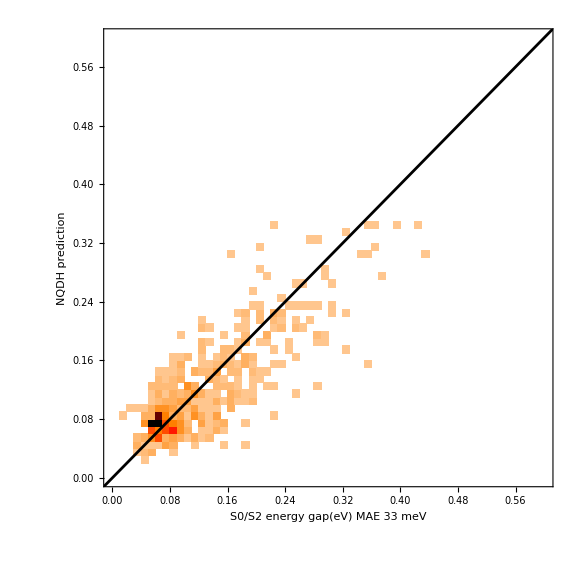

```mathematica
Show[
DensityHistogram[
g12,
50,
FrameStyle->myStyle[30],
FrameLabel->Table[Style[text,myStyle[30]],{text,{"S0/S2 energy gap(eV)\nMAE 33 meV","NQDH prediction"}}],
ImageSize->Large,
PlotRange->{{0,0.6},{0,0.6}},
ColorFunction->(Blend[{Lighter[Lighter[Orange]],Lighter[Orange],Orange,Red,Black},#]&)
],
Plot[x,{x,-100,100},PlotStyle->Black]
]
```

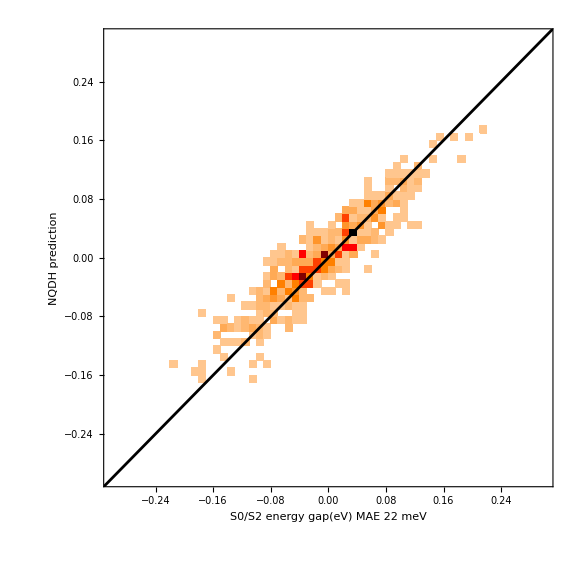

```mathematica
Show[
DensityHistogram[
dd,
50,
FrameStyle->myStyle[30],
FrameLabel->Table[Style[text,myStyle[30]],{text,{"S0/S2 energy gap(eV)\nMAE 22 meV","NQDH prediction"}}],
ImageSize->Large,
PlotRange->{{-0.3,0.3},{-0.3,0.3}},
ColorFunction->(Blend[{Lighter[Lighter[Orange]],Lighter[Orange],Orange,Red,Black},#]&)
],
Plot[x,{x,-100,100},PlotStyle->Black]
]
```

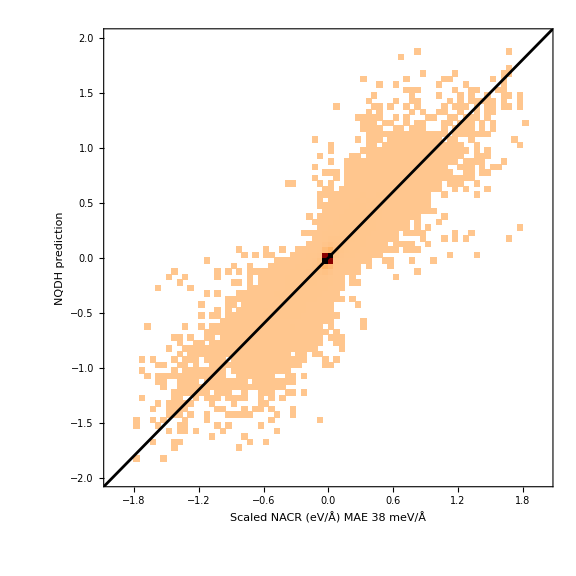

```mathematica
Show[
DensityHistogram[
q,
55,
FrameStyle->myStyle[20],
FrameLabel->Table[Style[text,myStyle[20]],{text,{"Scaled NACR (eV/Å)\nMAE 38 meV/Å","NQDH prediction"}}],
ImageSize->Large,
PlotRange->2{{-1,1},{-1,1}},
ColorFunction->(Blend[{Lighter[Lighter[Orange]],Lighter[Orange],Orange,Red,Black},#]&)
],
Plot[x,{x,-100,100},PlotStyle->Black]
]
```

```mathematica
BarLegend[{Blend[{Lighter[Lighter[Orange]],Lighter[Orange],Orange,Red,Black},#]&,{0,1}},4,LabelStyle->myStyle[20]]
```